```mathematica
(* First solve for the eigenvalues (energies) of the Simple Harmonic Oscillator SHO with omega =1 and mass=1 using a differential equation approach*)

h=1/√2;
V[x_]:=.5 x^2
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-13,13},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5}

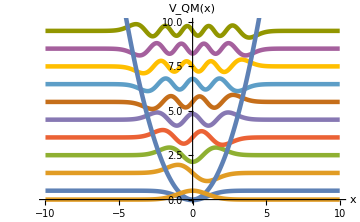

```mathematica
(* Next plot the potential, the eigenvalues and the eigenfunctions for the SHO *)

Show[Plot[Evaluate[-h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_QM(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[{V[x],.5Exp[-1/2 x^2]},{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{-10,10},{0,10}},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
(* Now we will use a Matrix approach to solve for the eigenvalues. This will map better to the quantum computer *)

(* First define the postion Matrix *)

Xp:=N[SparseArray[{i_,i_}->√((2π)/64)(2i-65)/2,{64,64}]]
```

```mathematica
(* Next define a special Matrix called the Sylvester Matrix that we will use to define the momentum Matrix *)

matpos:=Table[1/(√64)Exp[(2π)/64 ⅈ((2j-65)(2k-65))/4],{j,1,64},{k,1,64}]
```

```mathematica
(* Now define the momentum Matrix *)

Pp:=Chop[N[(ConjugateTranspose[matpos].Xp).matpos]]
```

```mathematica
(* Finally define the Matrix for the Hamiltonian for the SHO *)

Hpos:= .5 Pp.Pp+.5MatrixPower[Xp,2]
```

```mathematica
(* Now claculate the eigenvalues of the Hamiltonian *)

Reverse[N[Eigenvalues[Hpos]]]
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.4999,38.5002,39.4993,40.5015,41.4955,42.509,43.4753,44.5409,45.3951,46.6457,47.1836,48.8876,48.9127,50.7953,51.4606,53.2079,54.4213,56.2513,57.9406,60.0209,62.2377,64.733,67.6822,70.894,75.32,79.7297,89.896}

```mathematica
(* first ten match exactly with what we found solving the Schrodinger differential equation *)

(* It is to easy modify this for a different potential you are interested in*)

(* The next step is to export H in a format that the QISKIT VQE can read to find the lowest energy for H which should be approximately .5 *)
```

```mathematica
(* now let's try osc basis *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{16,16}]
```

SparseArray[…]

```mathematica
Xosc:=N[1/(√2)(s+Transpose[s])]
```

```mathematica
Posc:= ⅈ N[1/(√2)(-s+Transpose[s])]
```

```mathematica
Hquadraticosc := .5 Posc.Posc + .5 Xosc.Xosc
```

```mathematica
Reverse[N[Eigenvalues[Hquadraticosc]]]
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5}

```mathematica
(* Now let's try quartic *)
```

```mathematica
Hquarticosc := .5 Posc.Posc + .5 Xosc.Xosc + .01 MatrixPower[Xosc,4]
```

```mathematica
Reverse[N[Eigenvalues[Hquarticosc]]]
```

{0.507256,1.53565,2.59085,3.67109,4.77491,5.90103,7.04833,8.21119,8.29277,9.40278,10.6121,11.8273,13.1578,14.2906,17.3184,18.258}

```mathematica
1/2+3/4(.01)-21/8(.01)^2+333/16(.01)^3-30885/128(.01)^4
```

0.507256

```mathematica
(* Let's try sixth order polynomial *)
```

```mathematica
Hsixthosc := .5 Posc.Posc + .5 Xosc.Xosc + .001 MatrixPower[Xosc,6]
```

```mathematica
Reverse[N[Eigenvalues[Hsixthosc]]]
```

{0.501825,1.51248,2.54307,3.60389,4.70204,5.84185,7.0258,8.25469,8.46613,9.52736,10.8644,12.2126,13.9917,15.1122,22.8099,23.7201}

```mathematica
1/2+15/8(.001)-3495/64(.001)^2+1239675/256(.001)^3
```

0.501825

```mathematica
(* Let's try eighth order polynomial *)
```

```mathematica
Heighthosc := .5 Posc.Posc + .5 Xosc.Xosc + .0001 MatrixPower[Xosc,8]
```

```mathematica
Reverse[N[Eigenvalues[Heighthosc]]]
```

{0.500638,1.50558,2.52423,3.57116,4.66196,5.80916,7.02087,8.29485,8.62199,9.64173,11.1003,12.5481,15.3498,16.4268,35.3684,36.297}

```mathematica
1/2+105/16(.0001)-67515/32(.0001)^2
```

0.500635

```mathematica
(* Let's check with diff eq method *)
```

```mathematica
h=1/√2;
V[x_]:=.5 x^2+.0001 x^8
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-13,13},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.500638,1.50558,2.52423,3.57116,4.66195,5.80913,7.02075,8.30099,9.65148,11.0724}

```mathematica
h=1/√2;
V[x_]:=.5 x^2+.001 x^6
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-13,13},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.501825,1.51248,2.54307,3.60389,4.70204,5.84189,7.02575,8.25466,9.52877,10.8478}

0.5006351515625

```mathematica
h=1/√2;
V[x_]:=.5 x^2+.01 x^4
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-13,13},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.507256,1.53565,2.59085,3.67109,4.77491,5.90103,7.04833,8.21584,9.40269,10.6081}